Several models are loaded initially from sidecar object files, as well as from the example data.

```mathematica
<<CompiledFunctionTools`
SetDirectory[NotebookDirectory[]];

Models=<||>;
(* Import the meshes *)
AppendTo[Models,Association[
#->Import[#<>".stl"]&/@{
"Megathron","Thunderforge","AndromedaAscendant","Nostromo"
}]];
(* Discretize some example geometry *)
AppendTo[Models,Association[
#->DiscretizeGraphics[ExampleData[{"Geometry3D",#}]]&/@{
"StanfordBunny","Deimos"
}]];
```

```mathematica
DisplayGraphicsVoxelPlots=True;(* not used yet *)
```

## Asteroid Model Generation

## Isometric Views

```mathematica
MegathronModel;
{MeshRegion[%,ViewPoint->#,ImageSize->2000,
PlotRangePadding->0,Axes->True]}&/@{{0,0,Infinity},{0,-Infinity,0},{Infinity,0,0}};
TableForm[%]; (* Remove semi-colon to see the graphics *)
```

## Detailed Cuboid Plotting

Generating the coordinates for the sloped cuboids is done programmatically, then the coordinates are copied into the polygon and primitives definitions. This ensures that polygons can be regenerated later easily, while also removing the functional calls neessary for frequently called functionality.

```mathematica
Module[{FullCube,FullSlant,SlantSkeleton,SlantTop,SlantBottom},
(* The full set of points *)
FullCube=Flatten[Table[Select[Tuples[{-1,1},3]//Sort,#⟦i⟧==v&]⟦{1,2,4,3}⟧,{i,{1,2,3}},{v,{-1,1}}],1];
SlantTop=Map[If[And[#⟦1⟧==1,#⟦3⟧==1],{0,0,-1}+#,#]&,FullCube,{2}];

(* The slanted point set, discard the all-positive-X face *)
SlantSkeleton=Select[Flatten[Table[Select[Tuples[{-1,1},3]//Sort,#⟦i⟧==v&]⟦{1,2,4,3}⟧,{i,{1,2,3}},{v,{-1,1}}],1],DeleteDuplicates[#⟦All,1⟧]≠{1}&];
FullSlant=Map[If[And[#⟦1⟧==1,#⟦3⟧==1],{0,0,-2}+#,#]&,SlantSkeleton,{2}];
SlantBottom=Map[If[And[#⟦1⟧==-1,#⟦3⟧==1],{0,0,-1}+#,#]&,FullSlant,{2}];
(*Graphics3D/@Map[Polygon,{FullCube,FullSlant,SlantTop,SlantBottom},{2}];*)
{FullCube,FullSlant,SlantTop,SlantBottom}/2
]
```

{{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{1/2,-1/2,-1/2},{1/2,-1/2,1/2},{1/2,1/2,1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,1/2},{1/2,-1/2,1/2}}},{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,-1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}}},{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{1/2,-1/2,-1/2},{1/2,-1/2,0},{1/2,1/2,0},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,0},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,0},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,0},{1/2,-1/2,0}}},{{{-1/2,-1/2,-1/2},{-1/2,-1/2,0},{-1/2,1/2,0},{-1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,0},{1/2,-1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,0},{1/2,1/2,-1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,0},{-1/2,1/2,0},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}}}}

Using these coordinates, delayed mappings are built that take in an optional position parameter, and return the tensor Polygion[] objects. The functions available are: FullCube, FullSlope, SlopeTop, and SlopeBottom.

```mathematica
Clear[FullCube,FullSlope,SlopTop,SlopeBottom,SlopeCodeMapping,SlopeTypeMapping]
FullCube[Position:List[Repeated[_Real|_Integer|_Rational,{3}]],OptionsPattern[{Scale->{1,1,1},Forward->{1,0,0},Up->{0,0,1}}]]:=Translate[Scale[GeometricTransformation[Polygon[{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{1/2,-1/2,-1/2},{1/2,-1/2,1/2},{1/2,1/2,1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,1/2},{1/2,-1/2,1/2}}}],{OptionValue[Forward],
Cross[OptionValue[Up],OptionValue[Forward]],
OptionValue[Up]}//Transpose],OptionValue[Scale]],Position]
FullCube[P1:List[Repeated[_Real|_Integer|_Rational,{3}]],P2:List[Repeated[_Real|_Integer|_Rational,{3}]]]:=FullCube[Mean[{P1,P2}],Scale->Abs[P2-P1]]
FullCube[]:=FullCube[{0,0,0}]
FullSlope[Position:List[Repeated[_Real|_Integer|_Rational,{3}]],OptionsPattern[{Scale->{1,1,1},Forward->{1,0,0},Up->{0,0,1}}]]:=Translate[Scale[GeometricTransformation[Polygon[{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,-1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}}}],{OptionValue[Forward],
Cross[OptionValue[Up],OptionValue[Forward]],
OptionValue[Up]}//Transpose],OptionValue[Scale]],Position]
FullSlope[]:=FullCube[{0,0,0}]
SlopeTop[Position:List[Repeated[_Real|_Integer|_Rational,{3}]],OptionsPattern[{Scale->{1,1,1},Forward->{1,0,0},Up->{0,0,1}}]]:=Translate[Scale[GeometricTransformation[Polygon[{{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{-1/2,1/2,-1/2}},{{1/2,-1/2,-1/2},{1/2,-1/2,0},{1/2,1/2,0},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{1/2,-1/2,0},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,1/2,0},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,1/2},{-1/2,1/2,1/2},{1/2,1/2,0},{1/2,-1/2,0}}}],{OptionValue[Forward],
Cross[OptionValue[Up],OptionValue[Forward]],
OptionValue[Up]}//Transpose],OptionValue[Scale]],Position]
SlopTop[]:=FullCube[{0,0,0}]
SlopeBottom[Position:List[Repeated[_Real|_Integer|_Rational,{3}]],OptionsPattern[{Scale->{1,1,1},Forward->{1,0,0},Up->{0,0,1}}]]:=Translate[Scale[GeometricTransformation[Polygon[{{{-1/2,-1/2,-1/2},{-1/2,-1/2,0},{-1/2,1/2,0},{-1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,-1/2,0},{1/2,-1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,1/2,-1/2},{-1/2,1/2,0},{1/2,1/2,-1/2},{1/2,1/2,-1/2}},{{-1/2,-1/2,-1/2},{-1/2,1/2,-1/2},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}},{{-1/2,-1/2,0},{-1/2,1/2,0},{1/2,1/2,-1/2},{1/2,-1/2,-1/2}}}],{OptionValue[Forward],
Cross[OptionValue[Up],OptionValue[Forward]],
OptionValue[Up]}//Transpose],OptionValue[Scale]],Position]
SlopeBottom[]:=FullCube[{0,0,0}]
SlopeCodeMapping=<|
0->FullCube,16->SlopeBottom,18->SlopeTop,20->FullSlope
|>;
SlopeTypeMapping=Association[Reverse/@Normal[SlopeCodeMapping]];
```

The resulting Graphics3D objects, while not exactly primitives (do not have atomic heads, etc...), are satisfactory.

```mathematica
Graphics3D[{FullCube[],FullSlope[{0,1,0}],SlopeTop[{0,2,0}],SlopeBottom[{0,3,0}]}]
```

-Graphics3D-

It is critical that these objects be able to be oriented conveniently and precisely, which is provided by two optional patterns supported by the functions: Forward and Up. These parameters indicate that the forward and up directions be transformed to the specified vectors. It is an error to specify two vectors that are not perpendicular.

```mathematica
Graphics3D[{FullCube[],FullSlope[{0,1,0},Forward->{0,-1,0}],SlopeTop[{0,2,0},Up->{0,-1,0}],SlopeBottom[{0,3,0},Forward->{0,1,0},Up->{0,0,-1}]}]
```

-Graphics3D-

Additionally a Scale option is supported that takes in a list of three non-negative scaling factors. For the FullCube object, this scale factor can also be inferred from a two-argument form that specifies the bounds in each dimension (similar to the Cuboid two-argument form). The two argument form is without proper context for other shapes and so is not supported.

```mathematica
Grid[{{
FullCube[{0,0,0},{1,2,3}]//Graphics3D,
{FullCube[{0,0,0}],FullCube[{0,1,1},Scale->{3,1,2}]}//Graphics3D,
{FullSlope[{0,0,0},Scale->{1,2,3}]}//Graphics3D,
Graphics3D[SlopeTop[{5,0,0},Scale->{0.5,1.0,0.5}]],
Graphics3D[SlopeBottom[{5,0,0},Scale->{1.5,0.5,1.0}]]
}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

Note that FullSlope with a scaling factor of {1,1,1/2} is equivalent to SlopeBottom in shape, however does not represent the same position of the object relative to the specified origin making it more difficult to place correctly. In this way SlopeBottom is provided as a convenience in positioning.

```mathematica
Graphics3D[{FullSlope[{0,0,0},Scale->{1,1,1/2}],SlopeBottom[{0,1,0}]}]
```

-Graphics3D-

These can be used to replace Cuboid[] for a more flexible voxel plotting function: VoxelPlot. CuboidPlot is included for performance reasons when the desired plots are simple. As can be seen below, the CuboidPlot function is approximately 10x the speed of VoxelPlot. Timings are generated with RepeatedTiming[] for reliability.

```mathematica
CuboidPlot[Locations_,Size_]:=Graphics3D[Cuboid[#-Table[Size,{3}]/2,#+Table[Size,{3}]/2]&/@Locations,Boxed->False,ImageSize->Scaled[1.0]]
CuboidPlot[Locations_]:=CuboidPlot[Locations,1]
VoxelPlot[Locations_,Size_]:=Graphics3D[
If[Dimensions[#]=={3},
FullCube[#,Scale->{Size,Size,Size}],
#[[1]][#[[2,1]],Forward->#[[2,2]],Up->#[[2,3]]]
]&/@Locations,Boxed->False,ImageSize->Scaled[1.0]]
VoxelPlot[Locations_]:=VoxelPlot[Locations,1]
```

```mathematica
RandomInteger[{-10,10},{500,3}];
Grid[{
Prepend[CuboidPlot[%]//RepeatedTiming//{Quantity[#[[1]],"seconds"],#[[2]]}&,Text[Style["CuboidPlot","Section"]]],
Prepend[VoxelPlot[%]//RepeatedTiming//{Quantity[#[[1]],"seconds"],#[[2]]}&,Text[Style["VoxelPlot","Section"]]]
},ItemSize->{{12,6,20}}]
```

CuboidPlot | 0.004 s | 
VoxelPlot | 0.06 s |

### Voxel Plot Smoothing

Using these as building blocks, it is now possible to construct far smoother objects than with full cubes alone. This requires an ability to identify where they should be placed, in what orientation, and where not to place them. It is possible to degenerate the problem of adding blocks to a cuboid-only rendering of a mesh into a collection of one-dimensional decisions, reducing the conceptual complexity.

```mathematica
Clear[SlopeCheck,SlopeCheckC,SlopePrune,VoxelSmooth]
SlopeCheck[Pos_,F_,SA_]:=Module[{Adjacency},
(* There is permitted precisely one block surrouding the position given *)
(* Check around all the positions except along the Forward axis *)
If[Part@@Prepend[Pos,SA]≠0,
{{}},
Adjacency={Part@@Prepend[Pos+#,SA],#}&/@Flatten[# DeleteCases[UnitVector[3,#]&/@Range[3],Abs[F]]&/@{-1,1},1];
If[Total[Adjacency[[All,1]]]≠1,
{{}},
If[Length[Flatten[SlopeCheck[Pos+F,F,SA]]]≠0,
{
{1/2,SlopeTop,{Pos,F,-1Select[Adjacency,#[[1]]==1&][[1,2]]}},
{1/2,SlopeBottom,{Pos+F,F,-1Select[Adjacency,#[[1]]==1&][[1,2]]}}
},
{{1,FullSlope,{Pos,F,-1Select[Adjacency,#[[1]]==1&][[1,2]]}}}
]
]
]
]
SlopeCheckC=Compile[{{Pos,_Real,1},{F,_Real,1},{A,_Real,3}},
A⟦⟧
];
SlopeCheck[Pos_,SA_]:=
Flatten[SlopeCheck[Pos+#,#,SA]&/@Flatten[# (UnitVector[3,#]&/@Range[3])&/@{-1,1},1],1]
(* In the event that there are multiple slopes in the same position, take the lowest grade *)
SlopePrune[Slopes_]:=
Sort[#][[1,2;;]]&/@GatherBy[Slopes,#[[3,1]]&]
VoxelSmooth[Positions_]:=Module[{positions,sa,slopes},
positions=Function[{l,m},(#-m)&/@l][Positions,Min/@Transpose[Positions]+{-4,-4,-4}];
sa=Normal[SparseArray[#->1&/@positions,
Max[#]+3&/@Transpose[positions],0]];
slopes=SlopePrune[Select[Flatten[SlopeCheck[#,sa]&/@positions,1],Length[#]>0&]];
Join[positions,slopes]
]
```

```mathematica
RefinePrimitivesToPoints[MeshPrimitives[DiscretizeGraphics[Sphere[]],2][[All,1]],0.1,100];
Grid[
{{Graphics3D[Sphere[],Boxed->False,ImageSize->Scaled[1.0]],VoxelPlot[%],VoxelSmooth[%]//VoxelPlot}},
ItemSize->{{Scaled[1/3],Scaled[1/3],Scaled[1/3]}}
];
```

### Empyrion-Specific Data Codes

For export, specifically to Empyrion, the sloped components need to be mapped in a specific way, both block type, and block orientation.

```mathematica
(* Original mapping: Incorrect *)(*Clear[OrientationCodeMapping,OrientationVectorMapping]
OrientationVectorMapping=<|FromDigits["01",16]->{{0,+1,0},{0,0,+1}},FromDigits["09",16]->{{+1,0,0},{0,0,+1}},FromDigits["11",16]->{{0,-1,0},{0,0,+1}},FromDigits["19",16]->{{-1,0,0},{0,0,+1}},FromDigits["21",16]->{{0,+1,0},{+1,0,0}},FromDigits["29",16]->{{0,0,+1},{+1,0,0}},FromDigits["31",16]->{{0,-1,0},{+1,0,0}},FromDigits["39",16]->{{0,0,-1},{+1,0,0}},FromDigits["41",16]->{{0,-1,0},{0,0,-1}},FromDigits["49",16]->{{-1,0,0},{0,0,-1}},FromDigits["51",16]->{{0,+1,0},{0,0,-1}},FromDigits["59",16]->{{+1,0,0},{0,0,-1}},FromDigits["61",16]->{{0,+1,0},{-1,0,0}},FromDigits["69",16]->{{0,0,+1},{-1,0,0}},FromDigits["71",16]->{{0,-1,0},{-1,0,0}},FromDigits["79",16]->{{0,0,-1},{-1,0,0}},FromDigits["81",16]->{{0,0,+1},{0,-1,0}},FromDigits["89",16]->{{+1,0,0},{0,-1,0}},FromDigits["91",16]->{{0,0,-1},{0,-1,0}},FromDigits["99",16]->{{-1,0,0},{0,-1,0}},FromDigits["A1",16]->{{-1,0,0},{0,+1,0}},FromDigits["A9",16]->{{0,0,-1},{0,+1,0}},FromDigits["B1",16]->{{+1,0,0},{0,+1,0}},FromDigits["B9",16]->{{0,0,+1},{0,+1,0}}|>;OrientationCodeMapping=Association[Reverse/@Normal[OrientationVectorMapping]];*)
OrientationVectorMapping=<|177->{{0,0,-1},{1,0,0}},9->{{1,0,0},{0,1,0}},137->{{1,0,0},{0,0,-1}},89->{{1,0,0},{0,0,1}},33->{{0,0,1},{0,-1,0}},1->{{0,0,1},{0,1,0}},97->{{0,0,1},{-1,0,0}},81->{{0,-1,0},{0,0,1}},41->{{-1,0,0},{0,-1,0}},185->{{0,1,0},{1,0,0}},105->{{0,1,0},{-1,0,0}},129->{{0,1,0},{0,0,-1}},161->{{0,0,1},{1,0,0}},25->{{-1,0,0},{0,1,0}},153->{{-1,0,0},{0,0,-1}},73->{{-1,0,0},{0,0,1}},49->{{0,0,-1},{0,-1,0}},17->{{0,0,-1},{0,1,0}},113->{{0,0,-1},{-1,0,0}},65->{{0,1,0},{0,0,1}},57->{{1,0,0},{0,-1,0}},169->{{0,-1,0},{1,0,0}},121->{{0,-1,0},{-1,0,0}},145->{{0,-1,0},{0,0,-1}}|>;OrientationCodeMapping=Association[Reverse/@Normal[OrientationVectorMapping]];
```

```mathematica
Module[{hexstr},hexstr=Function[{n},"0x"<>StringJoin[StringTake[ToString[BaseForm[#,16]],1]&/@IntegerDigits[n,16,2]]];Grid[ArrayReshape[Function[{Vectors,Code},Graphics3D[{Thick,Total[{Red,Blue,Green}Abs[#]],Line[{{0,0,0},#}]}&/@Vectors,Boxed->False,Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-1,1},{-1,1},{-1,1}}]//Labeled[#,hexstr[Code]]&]@@#&/@Sort[Normal[OrientationCodeMapping],#1[[2]]<#2[[2]]&],{6,4},Null],ItemSize->{Scaled/@{1/4,1/4,1/4,1/4}}]
]
```

-Graphics3D-0x01 | -Graphics3D-0x09 | -Graphics3D-0x11 | -Graphics3D-0x19
-Graphics3D-0x21 | -Graphics3D-0x29 | -Graphics3D-0x31 | -Graphics3D-0x39
-Graphics3D-0x41 | -Graphics3D-0x49 | -Graphics3D-0x51 | -Graphics3D-0x59
-Graphics3D-0x61 | -Graphics3D-0x69 | -Graphics3D-0x71 | -Graphics3D-0x79
-Graphics3D-0x81 | -Graphics3D-0x89 | -Graphics3D-0x91 | -Graphics3D-0x99
-Graphics3D-0xa1 | -Graphics3D-0xa9 | -Graphics3D-0xb1 | -Graphics3D-0xb9

Converting the output of refinement and voxel smoothing steps in a format suitable for Empyrion Blueprints is accomplished by mapping Forward/Up vectors with the OrientationCodeMapping and SlopeTypeMapping associations. This is available in RemapBlockProperties that can be run on the output of VoxelSmooth.

```mathematica
Clear[RemapBlockProperties,RemapBlockProperties2]
RemapBlockProperties2[B:List[Repeated[_Integer,3]]]:=
Flatten[{B,0,1}]
RemapBlockProperties2[B:{_Symbol,{Repeated[{Repeated[_Integer,3]},3]}}]:=
Flatten[{B[[2,1]],SlopeTypeMapping[B[[1]]],OrientationCodeMapping[
B[[2,2;;3]]
]}]
RemapBlockProperties[B_]:=RemapBlockProperties2/@B
```

### Voxel Plot Filling

It is a separate problem identify the interior of the volume once the mesh has been converted to a point cloud subset of a lattice. The ray-stabbing method is used to cast rays through the voxel plot, tracking parity of the number of non-contiguous filled voxels. Odd parity indicates that the point is inside the volume, and even parity indicates an exterior point. This is performed along all three axes, and only points that are considered interior in all axes are part of the final interior volume.

To assist in visualizing the interiors of volumetric voxel plots, an interactive plotting function, SlicePlot, is included.

```mathematica
SlicePlot=Function[{Positions},
Manipulate[ArrayPlot[#⟦i⟧],{i,1,Length[#],1}]&[
SparseArray[#->1&/@(Function[{l,m},#-m&/@l][Positions,(Min/@Transpose[Positions])+{-1,-1,-1}])]
]
];
```

```mathematica
SlicePlot[RefinePrimitivesToPoints[MeshPrimitives[Models["StanfordBunny"],2][[All,1]],0.005]]
```

```mathematica
Clear[DisjointAccumulate,VoxelFill]
DisjointAccumulate=Function[{L},
BitAnd@@#&/@Transpose[{
If[#[[1]]==0,Join[Table[1,{Length[L]-Length[#]}],#],Table[1,Length[L]]]&[Split[Normal[L]][[-1]]],
BitOr@@#&/@Transpose[{Normal[L],Mod[Accumulate[Flatten[If[#[[1]]==0,#,Prepend[Table[0,{Length[#]-1}],1]]&/@Split[Normal[L]],1]]
,2]}]
}]
];
VoxelFill=Function[{VoxelPositions},Module[{Coords,SA,FilledVolume},
Coords=Function[{l,m},#-m&/@l][VoxelPositions,(Min/@Transpose[VoxelPositions])+{-1,-1,-1}];
SA=SparseArray[#->1&/@Coords];
FilledVolume=Transpose[Map[DisjointAccumulate,Transpose[SA,#],{2}],#]&/@{{1,2,3},{1,3,2},{3,2,1}};
Function[{l,m},#+m&/@l][Select[
ArrayRules[SparseArray[UnitStep[Total[FilledVolume]-3]]],
#[[2]]>0&
][[;;-2,1]],(Min/@Transpose[VoxelPositions])+{-1,-1,-1}]
]];
```

```mathematica
RefinePrimitivesToPoints[MeshPrimitives[Models["Megathron"],2][[All,1]],5,100];
Grid[{{
SlicePlot[%],
SlicePlot[VoxelFill[%]],
SlicePlot[VoxelFill[VoxelFill[%]]]
}}]
```

```mathematica
RefinePrimitivesToPoints[MeshPrimitives[Models["Megathron"],2][[All,1]],5,100];
Function[{l,m},#-m&/@l][%,(Min/@Transpose[%])+{-1,-1,-1}];
SparseArray[#->1&/@%];
Transpose[Map[DisjointAccumulate[#]&,Transpose[%,#],{2}],#]&/@{{1,2,3},{1,3,2},{3,2,1}};
Grid[{{SparseArray[UnitStep[Total[%]-3]]//ArrayRules[#][[;;-2,1]]&//CuboidPlot,CuboidPlot[RefinePrimitivesToPoints[MeshPrimitives[Models["Megathron"],2][[All,1]],5,100]]}}]
```

## Approximation of Boundary Meshes with Point Cloud Shells

The functions are written to be suitable for a “C” compilation target, resulting in highly efficient compiled library function calls. The function is also listable and parallelizable, ensuring minimal WVM calls.

A helper function prototype is also included that simplifies encoding the cutoff into the input tensors, converting triangles in ℝ^3 into quadrilaterlas in ℝ^3, encoding the resolution cutoff into the fourth point.

An additional function is included, RefinePrimitivesToPoints which ingests a primitive list, a resolution, and returns a list of points that represent the mesh boundary to within the given resolution. An overload of this function also takes a batch size, and significantly improves the efficiency of primitive refinement by performing it in parallel across threads on a smaller number of primitives per batch. This reduced batch size allows for more frequent rounding and unioning to keep the output point size smaller at any give point in the process.

Two CuboidPlot functions are included, one of which provides a simple single-argument signature suitable for standardized size plotting.

```mathematica
RefineTriangleC=Compile[{{Tri,_Real,2}},
Block[{P=Tri⟦1⟧,Q=Tri⟦2⟧,R=Tri⟦3⟧,Cutoff=Tri⟦4,1⟧,
Small,Large,Tris},
Tris={{P,Q,R}};
Small={0.};
Large={{P,Q,R}};
While[Length[Flatten[Large]]>0,
Tris=Flatten[Function[{P,Q,R},
Flatten[{
{#[[1]],Mean[#],Mean[{P,Q,R}]},
{Mean[#],#[[2]],Mean[{P,Q,R}]}
}&/@{{P,Q},{Q,R},{P,R}},1]][#⟦1⟧,#⟦2⟧,#⟦3⟧]&/@Large,1];
Small=Join[Small,Flatten[Select[Tris,
Max[Norm[Differences[#]⟦1⟧]&/@{{#⟦1⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧},{#⟦2⟧,#⟦3⟧}}]<Cutoff&]]];
Large=Select[Tris,
Max[Norm[Differences[#]⟦1⟧]&/@{{#⟦1⟧,#⟦2⟧},{#⟦1⟧,#⟦3⟧},{#⟦2⟧,#⟦3⟧}}]>Cutoff&];
];
Partition[Partition[Small⟦2;;-1⟧,3],3]
],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True
];
RefineTriangles[Tris_,Cutoff_]:=RefineTriangleC[Append[#,{Cutoff,0,0}]&/@Tris]
RefinePrimitivesToPoints[Primitives_,Resolution_]:=
DeleteDuplicates[Round[Round[Flatten[RefineTriangles[Primitives,Resolution],2],Resolution]/Resolution]]
RefinePrimitivesToPoints[Primitives_,Cutoff_,BatchSize_]:=
DeleteDuplicates[Flatten[ParallelMap[RefinePrimitivesToPoints[#,Cutoff]&,Partition[Primitives,BatchSize,BatchSize,{1,1},{}]],1]]
```

To test runtime performance, several benchmarks on a discretization of a sphere are performed, and indicates the dilation factor (relative to the vertex count of the original object). This dilation factor can be useful in estimating runtime of an operation when run on a real-world model.

```mathematica
Module[{Primitives,VertexCountOriginal},
Primitives=MeshPrimitives[DiscretizeGraphics[Sphere[]],2]⟦All,1⟧;
VertexCountOriginal=Flatten[Primitives,1]//DeleteDuplicates//Length;
Print["Input object vertex count: "<>ToString[VertexCountOriginal]];
Table[Flatten[{r,(RefinePrimitivesToPoints[Primitives,r]//Length)/VertexCountOriginal//N//RepeatedTiming}],{r,{1,0.5,0.1,0.05,0.02,0.01}}]
];
TableForm[%,
TableHeadings->{None,{"Spatial Resolution","Runtime (Seconds)","Vertex Dilation Factor"}}]
```

Input object vertex count: 642

Spatial Resolution | Runtime (Seconds) | Vertex Dilation Factor
1 | 0.012 | 0.0404984
0.5 | 0.012 | 0.115265
0.1 | 0.012 | 2.33333
0.05 | 0.26 | 10.0935
0.02 | 2. | 64.9751
0.01 | 14.2 | 262.028

The models loaded at the start of the notebook are available in a Models association, and so can be called up for rendering, statistics, and export.

Refining "StanfordBunny" to 25 blocks on the longest axis.

Effective resolution given length target is 0.00622796.

Original model dimensions: 0.155699 x 0.120673 x 0.154334

Original model triangle count: 69451

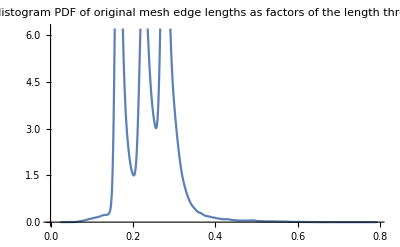

Time spent refining model: 1.56354 seconds

Time spent smoothing model: 0.43177 seconds

Resulting point count: 2994

Resulting point cloud dimensions: 25 x 19 x 25

Time spent exporting point cloud: 0.123227 seconds

```mathematica
Module[{ModelName="StanfordBunny",TargetSize=25,Model,ModelDimensions,RefinementTime,PointCloud,SmoothingTime,SmoothedPointCloud,ExportTime},
Print["Refining \""<>ModelName<>"\" to "<>ToString[TargetSize]<>" blocks on the longest axis."];
Model=Models[ModelName];
ModelDimensions=Max[#]-Min[#]&/@Transpose[MeshPrimitives[Model,0][[All,1]]];
Print["Effective resolution given length target is "<>ToString[Max[ModelDimensions]/TargetSize]<>"."];
Print["Original model dimensions: "<>StringJoin[Riffle[ToString/@ModelDimensions,{" x "," x "}]]];
Print["Original model triangle count: "<>ToString[Length[MeshPrimitives[Model,2][[All,1]]]]];
Print[SmoothHistogram[1/(Max[ModelDimensions]/TargetSize)Composition[Norm,Differences]/@MeshPrimitives[Model,1][[All,1]],ImageSize->Scaled[0.5],PlotLabel->"Histogram PDF of original mesh\nedge lengths as factors of the length threshold"]];
{RefinementTime,PointCloud}=RefinePrimitivesToPoints[MeshPrimitives[Model,2][[All,1]],Max[ModelDimensions]/TargetSize,100]//AbsoluteTiming;
{SmoothingTime,SmoothedPointCloud}=VoxelSmooth[PointCloud]//AbsoluteTiming;
Print["Time spent refining model: "<>ToString[Quantity[RefinementTime,"seconds"]]];
Print["Time spent smoothing model: "<>ToString[Quantity[SmoothingTime,"seconds"]]];
Print["Resulting point count: "<>ToString[Length[SmoothedPointCloud]]];
Print["Resulting point cloud dimensions: "<>ToString[
StringJoin[Riffle[ToString[Max[#]-Min[#]]&/@Transpose[PointCloud],{" x "," x "}]]
]];
ExportTime=AbsoluteTiming[Export[ModelName<>".csv",RemapBlockProperties[SmoothedPointCloud]]][[1]];
Print["Time spent exporting point cloud: "<>ToString[Quantity[ExportTime,"seconds"]]];
VoxelPlot[SmoothedPointCloud];
]
```

## Scratch

```mathematica
RefinePrimitivesToPoints[MeshPrimitives[DiscretizeGraphics[Sphere[]],2][[All,1]],0.1,100];
Export["Sphere.csv",VoxelSmooth[%]]
```

Sphere.csv

```mathematica
Max[#]-Min[#]&/@Transpose[MeshPrimitives[Models["Nostromo"],0][[All,1]]];
Export["Nostromo.csv",RemapBlockProperties[VoxelSmooth[RefinePrimitivesToPoints[MeshPrimitives[Models["Nostromo"],2][[All,1]],Max[%]/150,100][[All,{1,3,2}]]]]]//AbsoluteTiming
```

{104.864,Nostromo.csv}

```mathematica
Join[UnitVector[3,#]&/@Range[3],-UnitVector[3,#]&/@Range[3]];

MapIndexed[{SlopeBottom,Prepend[#,#2⟦1⟧{1,0,0}]}&,Flatten[Function[{up,forwards},{up,#}&/@forwards][#,DeleteCases[%,Abs[#]|-Abs[#]]]&/@%,1]];
Join[{
{FullCube,{{0,0,0},{1,0,0},{0,0,1}}},
{FullCube,{{0,0,1},{1,0,0},{0,0,1}}},
{FullCube,{{0,0,2},{1,0,0},{0,0,1}}},
{FullCube,{{0,1,0},{1,0,0},{0,0,1}}}},%];
Partition[%[[5;;,2,2;;]].{x,y,z},4]//MatrixForm
Export["Stick.csv",RemapBlockProperties[%%]]
```

((x
y) | (x
z) | (x
-y) | (x
-z)
(y
x) | (y
z) | (y
-x) | (y
-z)
(z
x) | (z
y) | (z
-x) | (z
-y)
(-x
y) | (-x
z) | (-x
-y) | (-x
-z)
(-y
x) | (-y
z) | (-y
-x) | (-y
-z)
(-z
x) | (-z
y) | (-z
-x) | (-z
-y))

Stick.csv

```mathematica
Module[{x={1,0,0},y={0,1,0},z={0,0,1}},
{
{-z,+x},{+x,+y},{+x,-z},{+x,+z},
{+z,-y},{+z,+y},{+z,-x},{-y,+z},
{-x,-y},{+y,+x},{+y,-x},{+y,-z},
{+z,+x},{-x,+y},{-x,-z},{-x,+z},
{-z,-y},{-z,+y},{-z,-x},{+y,+z},
{+x,-y},{-y,+x},{-y,-x},{-y,-z}
}
];
Join[UnitVector[3,#]&/@Range[3],-UnitVector[3,#]&/@Range[3]];
Flatten[Function[{up,forwards},{up,#}&/@forwards][#,DeleteCases[%,Abs[#]|-Abs[#]]]&/@%,1];
Association[#[[2]]->#[[1]]&/@Transpose[{%%%,OrientationCodeMapping/@%}]]
```

<|177→{{0,0,-1},{1,0,0}},9→{{1,0,0},{0,1,0}},137→{{1,0,0},{0,0,-1}},89→{{1,0,0},{0,0,1}},33→{{0,0,1},{0,-1,0}},1→{{0,0,1},{0,1,0}},97→{{0,0,1},{-1,0,0}},81→{{0,-1,0},{0,0,1}},41→{{-1,0,0},{0,-1,0}},185→{{0,1,0},{1,0,0}},105→{{0,1,0},{-1,0,0}},129→{{0,1,0},{0,0,-1}},161→{{0,0,1},{1,0,0}},25→{{-1,0,0},{0,1,0}},153→{{-1,0,0},{0,0,-1}},73→{{-1,0,0},{0,0,1}},49→{{0,0,-1},{0,-1,0}},17→{{0,0,-1},{0,1,0}},113→{{0,0,-1},{-1,0,0}},65→{{0,1,0},{0,0,1}},57→{{1,0,0},{0,-1,0}},169→{{0,-1,0},{1,0,0}},121→{{0,-1,0},{-1,0,0}},145→{{0,-1,0},{0,0,-1}}|>

```mathematica
OrientationVectorMapping=<|177->{{0,0,-1},{1,0,0}},9->{{1,0,0},{0,1,0}},137->{{1,0,0},{0,0,-1}},89->{{1,0,0},{0,0,1}},33->{{0,0,1},{0,-1,0}},1->{{0,0,1},{0,1,0}},97->{{0,0,1},{-1,0,0}},81->{{0,-1,0},{0,0,1}},41->{{-1,0,0},{0,-1,0}},185->{{0,1,0},{1,0,0}},105->{{0,1,0},{-1,0,0}},129->{{0,1,0},{0,0,-1}},161->{{0,0,1},{1,0,0}},25->{{-1,0,0},{0,1,0}},153->{{-1,0,0},{0,0,-1}},73->{{-1,0,0},{0,0,1}},49->{{0,0,-1},{0,-1,0}},17->{{0,0,-1},{0,1,0}},113->{{0,0,-1},{-1,0,0}},65->{{0,1,0},{0,0,1}},57->{{1,0,0},{0,-1,0}},169->{{0,-1,0},{1,0,0}},121->{{0,-1,0},{-1,0,0}},145->{{0,-1,0},{0,0,-1}}|>;OrientationCodeMapping=Association[Reverse/@Normal[OrientationVectorMapping]];
```

```mathematica
Hide
```